## COVID19 DATA

```mathematica
words = Take[Import["/Users/ruiz/Dropbox/Maria_sharing_paper/Clusters/BCR/Light_chain/antibody_lightchain.csv","Lines"]];
```

```mathematica
mat=Clip[Outer[DamerauLevenshteinDistance,words,words],{0,1},{0,0}];
```

```mathematica
nngr=AdjacencyGraph[mat];
```

```mathematica
EdgeRules[nngr];
```

```mathematica
bidirectedToUndirected=Join@@(GatherBy[EdgeList@#,Union]/.{x_,y_}:>{UndirectedEdge@@x})&;
```

```mathematica
g=Graph[%4,EdgeStyle->{Gray,Arrowheads[0]}];
```

```mathematica
a = Graphics[{EdgeForm[Directive[Dashed,Black]],ColorData["AvocadoColors"][0.5],Disk[]}];
```

```mathematica
b = Graphics[{EdgeForm[Directive[Thickness[0.2],Blue]],ColorData["AvocadoColors"][0.5],Disk[]}];
```

```mathematica
c = Graphics[{EdgeForm[Directive[Thickness[0.2],Pink]],ColorData["AvocadoColors"][0.5],Disk[]}];
```

```mathematica
d =  Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["GreenPinkTones"][0.7]]],ColorData["AvocadoColors"][0.5],Disk[]}];
```

```mathematica
e = Graphics[{EdgeForm[Directive[Dashed,Black]],ColorData["BrownCyanTones"][0.8],Disk[]}];
```

```mathematica
f =  Graphics[{EdgeForm[Directive[Thickness[0.2],Blue]],ColorData["BrownCyanTones"][0.8],Disk[]}];
```

```mathematica
g2= Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["FuchsiaTones"][0.5]]],ColorData["BrownCyanTones"][0.8],Disk[]}];
```

```mathematica
h= Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["FruitPunchColors"][0.1]]],ColorData["BrownCyanTones"][0.8],Disk[]}];
```

```mathematica
i = Graphics[{EdgeForm[Directive[Thickness[0.2],Black]],ColorData["BrownCyanTones"][0.8],Disk[]}];
```

```mathematica
j = Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["FuchsiaTones"][0.5]]],ColorData["BrownCyanTones"][0.8],Disk[]}];
```

```mathematica
k = Graphics[{EdgeForm[Directive[Dashed,Black]],Red,Disk[]}];
```

```mathematica
l = Graphics[{EdgeForm[Directive[Thickness[0.2],Blue]],Red,Disk[]}];
```

```mathematica
m = Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["FuchsiaTones"][0.5]]],Red,Disk[]}];
```

```mathematica
n = Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["FruitPunchColors"][0.1]]],Red,Disk[]}];
```

```mathematica
o = Graphics[{EdgeForm[Directive[Thickness[0.2],Black]],Red,Disk[]}];
```

```mathematica
p = Graphics[{EdgeForm[Directive[Thickness[0.2],Brown]],Red,Disk[]}];
```

```mathematica
q= Graphics[{EdgeForm[Directive[Dashed,Black]],White,Disk[]}];
```

```mathematica
r= Graphics[{EdgeForm[Directive[Thickness[0.2],Blue]],White,Disk[]}];
```

```mathematica
s= Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["AvocadoColors"][0.5]]],White,Disk[]}];
```

```mathematica
t = Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["FruitPunchColors"][0.1]]],White,Disk[]}];
```

```mathematica
u= Graphics[{EdgeForm[Directive[Thickness[0.2],Black]],White,Disk[]}];
```

```mathematica
v = Graphics[{EdgeForm[Directive[Thickness[0.2],Pink]],White,Disk[]}];
```

```mathematica
w= Graphics[{EdgeForm[Directive[Thickness[0.2],Red]],White,Disk[]}];
```

```mathematica
x = Graphics[{EdgeForm[Directive[Thickness[0.2],ColorData["BrownCyanTones"][0.8]]],White,Disk[]}];
```

```mathematica
y = Graphics[{EdgeForm[Directive[Dashed,Black]],ColorData["AvocadoColors"][1],Disk[]}];
```

```mathematica
opts= {VertexShape->{3|4|6|11|15|52|79|80|81|84|86|87|93|104|106|107|121|122|143|145|147|151->a,50|62|88->b, 85|90|91|92->c,95|133->d,8|18|34|72|76|94|99|109|110|113|128|150->e,101->f,17|23|31|39|43|138|141->g2,35|129|131|142->h,33|37->i,47->j,9|28|74|103|114|115|118|119|149->k,137->l,19|26|27|29|41|42|45|134|139->m,125->n,12|21|32->o,38->p,1|2|7|10|13|20|24|46|51|53|69|77|78|82|96|100|105|111|117|120|132|144|146|152->q,5|49|54|55|56|57|58|59|60|61|63|64|65|66|67|68|70|89->r,14|30|36|40|98|116|124|136|148->s,126|130->t,16|22|25|44|97|102|108|135|140->u,48->v,123->w,127->x,71|73|75|83|112->y},VertexSize -> {2|5|6|8|9|11|12|13|15|16|17|20|23|24|26|27|28|30|33|34|38|41|42|44|46|47|51|52|55|56|57|60|63|69|71|73|74|76|78|81|84|86|88|90|96|97|98|99|104|106|107|109|111|114|115|116|118|120|121|126|133|134|135|137|138|140|141|143|144|145|146|147|150|152->0.5, 1|3|7|10|14|18|29|35|37|40|49|50|59|61|67|75|79|85|95|101|102|103|108|117|119|123|124|129|132|136|139|142|148->0.7,19|25|32|39|43|45|48|62|64|66|72|87|105|110|122|125|128->0.9,4|22|31|58|68|77|80|82|83|92|94|113|127|131->1.1,91|93|151->1.3,21|89|100|130->1.5,70|112->1.7,53|54|149->1.9,65->2.1} ,EdgeStyle->{Gray,Arrowheads[0]}};
```

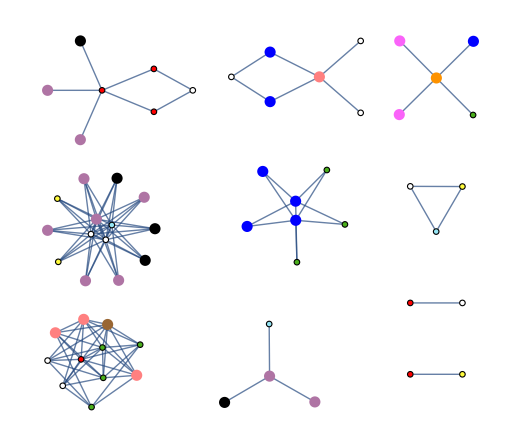

```mathematica
Graph[g,bidirectedToUndirected@g,opts]
```

```mathematica
Export["/Users/ruiz/Dropbox/Maria_sharing_paper/Clusters/BCR/Light_chain/graph_LC.pdf",%143];
```